### Start choosing the example:

```mathematica
t=11;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6},{1,3,4,S7},{4,3,1,S8},{1,3,2,S9},{2,3,1,S10},{3,4,2,S11},{2,4,3,S12},{2,3,4,S13},{4,3,2,S14},{3,1,2,S15},{2,1,3,S16}}|>

```mathematica
Data["Switching Costs"]={};
```

#### This should take around 40 min....

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U2-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 4.69909 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{5.24871,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j617→1.,j618→1.,j619→0,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0.,j626→0.,j627→0.,j628→0,j629→0.,j630→0.,jt631→0,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0,jt638→1.,jt639→0.,jt640→0.,jt641→0.,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0,jt652→1.,jt653→0.,jt654→0.,u655→2.,u656→2.,u657→1.,u658→1.,u659→1.,u660→0.,u661→2.,u662→1.,u663→1.,u664→1.,u665→0.,u666→0.,u667→0.,u668→2.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→1.41151,u656→1.41151,u657→0.705756,u658→0.705756,u659→0.705756,u660→0.,u661→1.41151,u662→0.705756,u663→0.705756,u664→0.705756,u665→0.,u666→0.,u667→0.,u668→1.41151|>

```mathematica
Min[Select[{Indeterminate,0.1},!(#=== Indeterminate)&]]
```

0.1

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→1.4537,u656→1.4537,u657→0.72685,u658→0.72685,u659→0.72685,u660→0.,u661→1.4537,u662→0.72685,u663→0.72685,u664→0.72685,u665→0.,u666→0.,u667→0.,u668→1.4537|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→1.54642,u656→1.54642,u657→0.773209,u658→0.773209,u659→0.773209,u660→0.,u661→1.54642,u662→0.773209,u663→0.773209,u664→0.773209,u665→0.,u666→0.,u667→0.,u668→1.54642|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→1.9184,u656→1.9184,u657→0.959201,u658→0.959201,u659→0.959201,u660→0.,u661→1.9184,u662→0.959201,u663→0.959201,u664→0.959201,u665→0.,u666→0.,u667→0.,u668→1.9184|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.22045×10^-15

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.,u656→2.,u657→1.,u658→1.,u659→1.,u660→0.,u661→2.,u662→1.,u663→1.,u664→1.,u665→0.,u666→0.,u667→0.,u668→2.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.1882,u656→2.1882,u657→1.0941,u658→1.0941,u659→1.0941,u660→0.,u661→2.1882,u662→1.0941,u663→1.0941,u664→1.0941,u665→0.,u666→0.,u667→0.,u668→2.1882|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.55799,u656→2.55799,u657→1.27899,u658→1.27899,u659→1.27899,u660→0.,u661→2.55799,u662→1.27899,u663→1.27899,u664→1.27899,u665→0.,u666→0.,u667→0.,u668→2.55799|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.71476,u656→2.71476,u657→1.35738,u658→1.35738,u659→1.35738,u660→0.,u661→2.71476,u662→1.35738,u663→1.35738,u664→1.35738,u665→0.,u666→0.,u667→0.,u668→2.71476|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.71493,u656→2.71493,u657→1.35746,u658→1.35746,u659→1.35746,u660→0.,u661→2.71493,u662→1.35746,u663→1.35746,u664→1.35746,u665→0.,u666→0.,u667→0.,u668→2.71493|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→3.65335,u656→3.65335,u657→1.82668,u658→1.82668,u659→1.82668,u660→0.,u661→3.65335,u662→1.82668,u663→1.82668,u664→1.82668,u665→0.,u666→0.,u667→0.,u668→3.65335|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.72317,u656→2.72317,u657→1.36159,u658→1.36159,u659→1.36159,u660→0.,u661→2.72317,u662→1.36159,u663→1.36159,u664→1.36159,u665→0.,u666→0.,u667→0.,u668→2.72317|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.73164,u656→2.73164,u657→1.36582,u658→1.36582,u659→1.36582,u660→0.,u661→2.73164,u662→1.36582,u663→1.36582,u664→1.36582,u665→0.,u666→0.,u667→0.,u668→2.73164|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.74876,u656→2.74876,u657→1.37438,u658→1.37438,u659→1.37438,u660→0.,u661→2.74876,u662→1.37438,u663→1.37438,u664→1.37438,u665→0.,u666→0.,u667→0.,u668→2.74876|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.8016,u656→2.8016,u657→1.4008,u658→1.4008,u659→1.4008,u660→0.,u661→2.8016,u662→1.4008,u663→1.4008,u664→1.4008,u665→0.,u666→0.,u667→0.,u668→2.8016|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→2.89499,u656→2.89499,u657→1.4475,u658→1.4475,u659→1.4475,u660→0.,u661→2.89499,u662→1.4475,u663→1.4475,u664→1.4475,u665→0.,u666→0.,u667→0.,u668→2.89499|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.44089×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→3.10493,u656→3.10493,u657→1.55247,u658→1.55247,u659→1.55247,u660→0.,u661→3.10493,u662→1.55247,u663→1.55247,u664→1.55247,u665→0.,u666→0.,u667→0.,u668→3.10493|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→3.3534,u656→3.3534,u657→1.6767,u658→1.6767,u659→1.6767,u660→0.,u661→3.3534,u662→1.6767,u663→1.6767,u664→1.6767,u665→0.,u666→0.,u667→0.,u668→3.3534|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j617→1.,j618→1.,j619→0.,j620→1.,j621→1.,j622→2.,j623→2.,j624→0.,j625→0,j626→0,j627→0,j628→0,j629→0.,j630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→1.,jt636→1.,jt637→0.,jt638→1.,jt639→0.,jt640→0.,jt641→0,jt642→0.,jt643→0.,jt644→1.,jt645→0.,jt646→0.,jt647→0,jt648→0.,jt649→0.,jt650→1.,jt651→0.,jt652→1.,jt653→0.,jt654→0.,u655→3.65335,u656→3.65335,u657→1.82668,u658→1.82668,u659→1.82668,u660→0.,u661→3.65335,u662→1.82668,u663→1.82668,u664→1.82668,u665→0.,u666→0.,u667→0.,u668→3.65335|>

### What we this plot for?

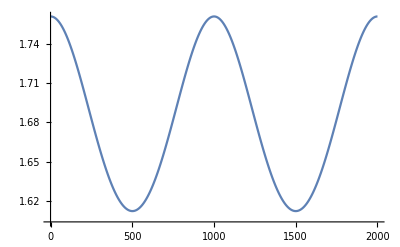

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.